```mathematica
Box2g[u_]:=Rectangle[{Min[First[u]],Min[Last[u]]},{Max[First[u]],Max[Last[u]]}];
Box2g[ix_,iy_,u_]:=Module[{value,min,max,mid},
value={u[[ix]],u[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{Rectangle[min,max],PointSize[Large],Red,Point[mid]}
];

Pped2g[ix_,iy_, pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Large],Red,Point[x1]}
];

PpedD2g[ix_,iy_,pped2[x_,m_,u_, n_, v_]]:= Module[{x1,m1,u1,n1,v1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
n1={{n[[ix,ix]], n[[ix,iy]]},{n[[iy,ix]], n[[iy,iy]]}};
v1={v[[ix]], v[[iy]]};
(*GeometricTransformation[Rectangle[{Min[First[u1]]+Min[First[v1]],Min[Last[u1]]+Min[Last[v1]]},{Max[First[u1]]+Max[First[v1]],Max[Last[u1]]+Max[Last[v1]]}],AffineTransform[{m1,x1}]]];*)
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Large],Red,Point[x1]}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<tmp.dat;
```

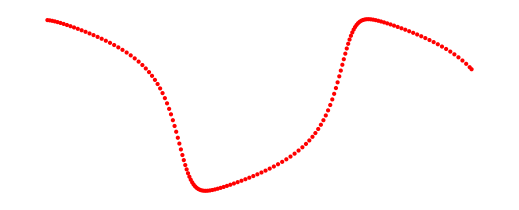

```mathematica
Graphics[Pped2g[1,2,#]& /@ list]
```

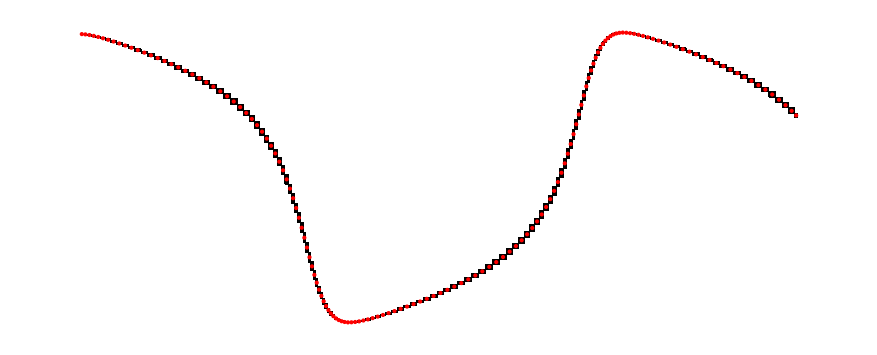

```mathematica
Graphics[Box2g[1,3,#]& /@ list]
```

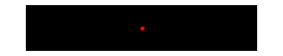

```mathematica
Graphics[Box2g[1,3,list[[2]]]]
```

```mathematica
Graphics[Join[{EdgeForm[{Thick,Blue}],FaceForm[Pink]},Box2g /@ ({#[[1]],#[[2]]}& /@ list) ],AspectRatio->1/1]
```

-Graphics-

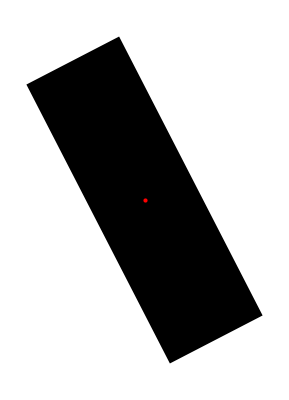

```mathematica
Graphics[Pped2g[1,2,pped[{1.539186803229428,0.7942946460630196},{{-0.8886499144836875,-0.4585862274486874},{-0.45858622906508495,0.8886499153178268}},{{-5.777974964630873*^-7,5.77797496606545*^-7},{-1.7328489290783917*^-6,1.7328489296351884*^-6}}]]]
```

```mathematica
Graphics[Pped2g[1,2,pped[{Interval[{1.53,1.531}],Interval[{0.79,0.8}]},{{Interval[{-0.89,-0.88}],Interval[{-0.46,-0.45}]},{Interval[{-0.46,-0.45}],Interval[{0.88,0.89}]}},{{-5.777974964630873*^-7,5.77797496606545*^-7},{-1.7328489290783917*^-6,1.7328489296351884*^-6}}]]]
```

-Graphics-

```mathematica
pped2ins=pped2[{0.93698668810247299,0.02834184244361777,-0.43838728724406478,0.09077192969458737},{{-0.99264500031103386,0.01902748548671305,-0.02166939301075582,0.10013070138346961},{0.03238927627977776,-0.05951531394638056,-0.99266444724710134,0.83185601928842989},{0.10771485939523606,0.54165824236675553,0.05494925582050147,0.53307139320540520},{0.04476993639760738,-0.83827336273919262,0.10549081411633730,-0.00000000000000000}},{{-0.00000000000237820,0.00000000000255149},{-0.00000000000001624,0.00000000000002958},{-0.00000000009251626,0.00000000009335877},{-0.00000000000000983,0.00000000000001825}},{{5.57584429162345430,0.02693324178592341,-0.09299368486560319,58.22588146149444555},{10.70847012518644448,0.04968500918041528,0.25874186406955113,-522.55666625886794918},{23.62964779547518646,0.10306235565193000,-2.38686145530664362,816.40453730199703841},{89.60316835659230605,0.41938219740047572,3.75146953965977170,-17.98311023846477497}},{{-0.00000000000000000,0.00000000000000000},{-0.00000000000000000,0.00000000000000000},{-0.00000000000000000,0.00000000000000000},{-0.00000000000000000,0.00000000000000000}}];
Graphics[PpedD2g[1,2,pped2ins],AspectRatio->1/1]
```

-Graphics-

```mathematica
Graphics[Join[{EdgeForm[{Thick,Blue}]},Pped2g[1,2,#]& /@ (<<pped.dat) ],AspectRatio->1/1]
```

-Graphics-

```mathematica
Graphics[Join[{EdgeForm[{Thick,Blue}]},Pped2g[1,2,pped[{0.98194293455087323,0.01415136035747279,-1.00773313337103598,0.60328796867331125},{{0.20636131584097564,0.02416881432459777,0.00062311546543543,0.17849665697144934},{-0.23382619613552039,-0.00048210936751883,0.02303381130639201,109.41222213595965229},{7.71842568894271253,1.03230297152651684,0.04970723358768088,5.22293125028114158},{-53.58043230095294263,-0.04470436886281197,0.98283158255770853,1.62529662882284875}},{{1618900.19717572606168687,1972737.19059469224885106},{-130753.22013105772202834,20921.00217204144428251},{-150553047.05083608627319336,-119092974.33915629982948303},{-12778908.28464674390852451,-8726462.54407251998782158}}]] ],AspectRatio->1/1]
```

-Graphics-

```mathematica
Graphics[Join[{ EdgeForm[{Thick,Blue}]},PpedD2g[1,2,#]& /@ list ],AspectRatio->1/1]
```

-Graphics-

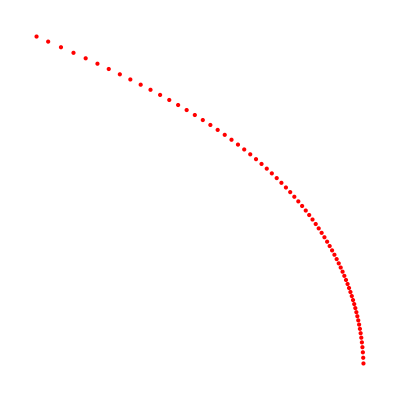

```mathematica
Graphics[Join[{ EdgeForm[{Thick,Blue}]},PpedD2g[1,2,#]& /@ (<<pped2.dat) ],AspectRatio->1/1]
```

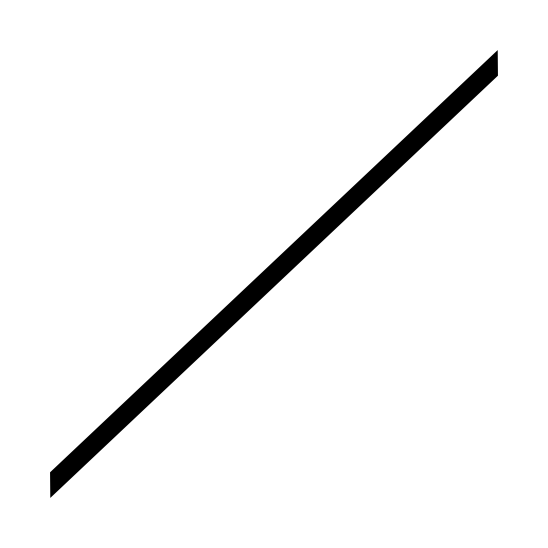

```mathematica
Graphics[PpedD2g[1,2,
pped2[{0.92986836934679873,0.02979235758901632,-0.38906260419083388,0.07845315010315794},{{-0.98972752633891703,0.02724070549102208,0.03766094556127106,0.13365161248804203},{-0.02126726319149336,-0.06960972363444283,-0.98835187882212805,0.80215902090672342},{0.12799973560096273,0.57960790432429288,0.06489722728167649,0.56603810022513368},{0.06002661750821049,-0.81145986196773101,0.13240304641266484,-0.00000000000000000}},

{{-0.000223630,0.00240070},
{-0.00001723,0.00003144},
{-0.09924894,0.10016988},
{-0.0001095,0.0002026}},

{{5.95728490223289686,0.02860220508002136,-0.13715352467375605,72.51872758226990356},{12.15780853469727951,0.05646345892463279,0.32454565630130311,-596.30028038142859259},{20.86794189744070493,0.09161017242624636,-2.72848896381584805,841.47062613508501272},{78.83175379878714750,0.36844570245914759,3.88051612491821674,-27.64186804497332872}},

{{-0.00000000000000000,0.00000000000000000},{-0.00000000000000000,0.00000000000000000},
{-0.00000000000000000,0.00000000000000000},{-0.00000000000000000,0.00000000000000000}}]
],AspectRatio->1/1]
```